# Transfer Function

```mathematica
Quit[]
```

## Mock Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[16]; (* To use all the available kernels *)
```

### Data

```mathematica
DataTransferFunction=Import["Transfer_Function.txt","Data"]//Quiet; (* Data from CLASS (python): {k, ωb, ωm} *)
Length[DataTransferFunction]/114//N (* There are 16 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each pair {ωb, ωm}*)
(* Normalized data to get T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,(#⟦4⟧)/Max[PartData⟦i,1,4⟧]}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Drop[Join@@NormPartData,{1,-1,2}]; (* Re-Join the datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

16.

{912,4}

### BBKS Fitting Formula

```mathematica
(* Various parameters *)
cH0 = 2997.92458; (* c/H0 [h^-1 Mpc] *)
Tcmb = 2.7255; (* CMB temperature [K] *)
h=0.67810; (* Reduced Hubble constant *)
Neff=3.046; (* Effective number of relativistic degrees of freedom *)
KtoeV = 8.621738*10^-5; (* Conversion from K to eV *)
(* BBKS: CDM >> Baryons, adiabatic fluctuations *)
ρcr[h_]:=8.098*10^-11 h^2; (* Critical density *)
Ωγ[h_]:=π^2/30 gγ*T^4/ρcr[h]/.T->Tcmb K/.gγ->2/.GeV->10^9/.K->KtoeV; (* Radiation density parameter *)
Ων[h_,Neff_]:=Neff*7/8 (4/11)^(4/3)Ωγ[h] (* Neutrinos density parameter *)
θ[h_,Neff_]:=(Ωγ[h]+Ων[h,Neff])/(1.68 Ωγ[h]) (* Measure of ρr/ργ *)
qBBKS[k_,ωb_,ωm_,h_,Neff_]:=(k*θ[h, Neff]^(1/2))/(ωm - ωb)
(* Transfer function for CDM *)
TcBBKS[k_,ωb_,ωm_,h_,Neff_]:=Log[1+2.34 qBBKS[k,ωb,ωm,h,Neff]]/(2.34 qBBKS[k, ωb, ωm, h, Neff])(1+3.89qBBKS[k,ωb,ωm,h,Neff] + (16.1 qBBKS[k,ωb,ωm,h,Neff])^2+(5.46 qBBKS[k,ωb,ωm,h,Neff])^3+(6.71 qBBKS[k,ωb,ωm,h,Neff])^4)^(-1/4)
(* BBKS: Non neglecteing baryons *)
RJr[ωb_,ωm_]:=1.6 (ωm-ωb)^(-1/2) (* Small scale filter [kpc] *)
TcbBBKS[k_,ωb_,ωm_,h_,Neff_]:=TcBBKS[k,ωb,ωm,h,Neff] (1+((10^-3*k*RJr[ωb, ωm])^2)/2)^-1 (* Transfer function for CDM + baryons *)
```

### Eisenstein-Hu Fitting Formula

All the formulas are extracted from EH97I  [9709112 v1] paper, unless stated.

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)

(* See Eq. (11) *)
a1[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1[ωm]^(-ωb/ωm)*a2[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1[ωm](((ωm - ωb)/ωm)^b2[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeq[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keq[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
q[k_,ωm_] := k/(13.41 keq[ωm])  (* See Eq. (10) *)
R[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeq[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
G[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
ksilk[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
(* Sound horizon at drag epoch -> See Eq. (6) *)
s[ωb_,ωm_]:=2/(3 keq[ωm])√(6/R[zeq[ωm],ωb])Log[(√(1+R[zd[ωb,ωm],ωb])+√(R[zd[ωb,ωm],ωb]+R[zeq[ωm],ωb]))/(1+√R[zeq[ωm],ωb])]
st[k_,ωb_,ωm_]:=s[ωb,ωm]/((1+(βnode[ωm]/(k*s[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keq[ωm]*s[ωb,ωm] (1+R[zd[ωb,ωm],ωb])^(-3/4)G[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
f[k_,ωb_,ωm_]:=1/(1 + ((k*s[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*q[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*q[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*q[k,ωm]]+Cf[k,ωb,ωm]*q[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*q[k,ωm]]/(Log[E+1.8*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=f[k,ωb,ωm]*T01[k,ωb,ωm]+(1-f[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*s[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)ⅇ^(-(k/ksilk[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
length=4; depth=4; (* Number of nucleotides and genes. Chromosomes will be 4x4 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,9}; (* Power of x *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{x->#1,y->#2,z->#3})&; (* Individual *)
temp=Mean[Table[Abs[MockData⟦i,4⟧-ft[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧]]/MockData⟦i,4⟧*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4]]; (* If rep⟦2⟧ == 4 -> modify the power of x *)
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals": Σ r f((ax)^l(by)^m(cx)^n) -> See Eq. (10) *)
funcGA[x_,y_,z_,kid_,gram_]:=Sum[kid⟦i,1⟧ gram⟦kid⟦i,2⟧⟧@((kid⟦i,3⟧x)^kid⟦i,4⟧),{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4]},{pop},{length}];
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for a function which is positive, goes to 1 when k -> 0, and k lives in a log-space -> See Eq. (9) *)
Do[
pigs=(1+funcGA[(2.3481818868485798 x)/(-y+z),y,z,#,grammar])^(-1/4)&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=150;
SaveState={};
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.7,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 65.395844

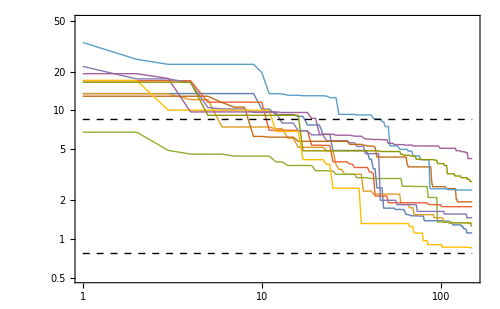

```mathematica
(* Plot the accuracy of GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1,generations},{0.5,50}},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,PlotStyle->Thick,ImageSize->500,
Epilog->{{Dashed,Line[{{1,8.5},{generations,8.5}}//Log],Line[{{1,0.77},{generations,0.77}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.75,0.2}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.11}]]}]
```

```mathematica
DataSaved=Import["Save_State.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-0.854517,9872}

```mathematica
AccGA[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧] (* Accuracy of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.y->0.022/.z-> 0.11,x->0] (* Correct limits of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.y->0.022/.z-> 0.11,x->∞]
```

0.854517

1.

0.

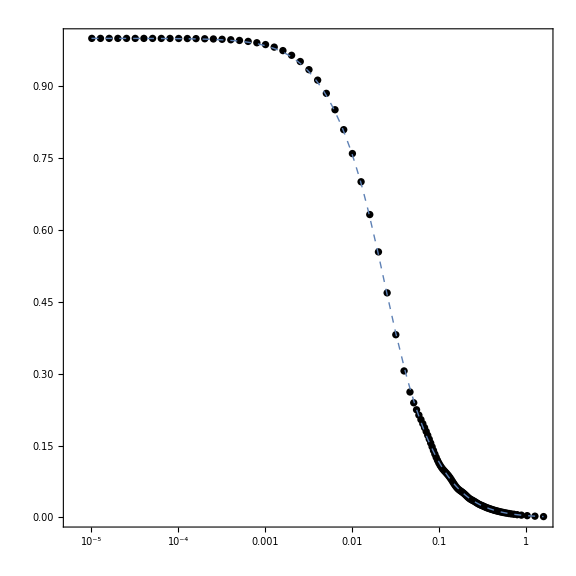

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.y->NormPartData⟦5⟧⟦1,2⟧/.z->NormPartData⟦5⟧⟦1,3⟧}//Evaluate,{x,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦5⟧⟦i,1⟧,NormPartData⟦5⟧⟦i,4⟧},{i,1,Length[NormPartData⟦5⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick,Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->Large]
```

### Long Run For the Winner

```mathematica
generations=10000;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[9872,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 2504 secs or 42 mins

Accuracy = 0.815012

Best-fit function is:

1/((1+59.0998 (x/(-y+z))^1.49177+4658.01 (x/(-y+z))^4.02755+3170.79 (x/(-y+z))^6.06+150.089 (x/(-y+z))^7.28478)^(1/4))

```mathematica
(* Check the correct limits of the GA solution *)
Limit[GApop⟦-1,2⟧/.y->0.022/.z->0.11,x->0]
Limit[GApop⟦-1,2⟧/.y->0.022/.z->0.11,x->∞]
```

1.

0.

```mathematica
AccGA[GApop⟦-1,2⟧]
AccGA[TEH[x*h,y,z]]
AccGA[TcbBBKS[x*h,y,z,h,Neff]]
```

0.815012

0.777504

8.70957

```mathematica
Export["Accuracy_Evolution.txt",GApop⟦All,1⟧,"Table"];
```

### Plots

```mathematica
Winner[x_,y_,z_]:=1/((1+59.09983473000389 (x/(-y+z))^1.4917653903428132+4658.007645250978 (x/(-y+z))^4.027553399922359+3170.788890492977 (x/(-y+z))^6.0600043498512886+150.08874315951203 (x/(-y+z))^7.284778673036612)^(1/4))
```

```mathematica
DataAccuracy=Import["Accuracy_Evolution.txt","Data"]//Flatten;
```

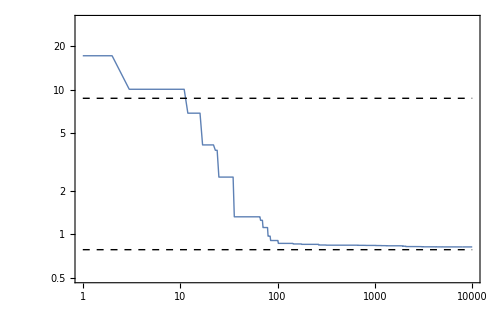

```mathematica
(* Plot of χ^2 over the generations -> We should modify the configuration of the GA *)
generations=10000;
ListLogLogPlot[DataAccuracy//Abs,Joined->True,
PlotRange->{{1,generations},{0.5,30}},PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500,
Epilog->{{Dashed,Line[{{1,8.7},{generations,8.7}}//Log],Line[{{1,0.78},{generations,0.78}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.8,0.75}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.17}]]}]
```

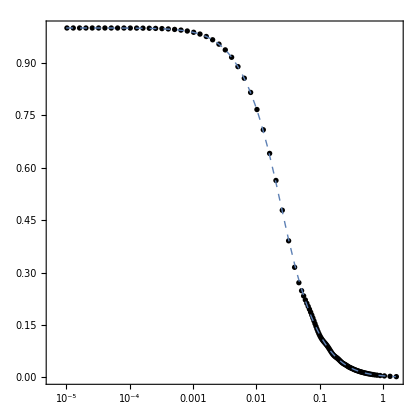

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[Winner[x,y,z]/.y->NormPartData⟦10⟧⟦1,2⟧/.z->NormPartData⟦10⟧⟦1,3⟧//Evaluate,{x,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->420]
```

```mathematica
(* Accuracy for each T(k); there are 16 datasets *)
AccuracyWinner=Table[Mean[Table[{Abs[NormPartData⟦j⟧⟦i,4⟧-Winner[NormPartData⟦j⟧⟦i,1⟧,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧]]/(NormPartData⟦j⟧⟦i,4⟧)*100},{i,1,Length[NormPartData⟦j⟧]}]],{j,1,Length[NormPartData]}]
```

{{0.904959},{0.8165},{0.771501},{0.752605},{0.897335},{0.800334},{0.740871},{0.721048},{0.921556},{0.825905},{0.753583},{0.725033},{1.00389},{0.913911},{0.838216},{0.798157}}

## Comparison

```mathematica
accBBKS=Table[{MockData⟦i,1⟧,100*Abs[(1-TcbBBKS[MockData⟦i,1⟧*h,MockData⟦i,2⟧,MockData⟦i,3⟧,h,Neff]/MockData⟦i,4⟧)]},{i,1,Length[MockData]}]; 
accEH=Table[{MockData⟦i,1⟧,100*Abs[(1-TEH[MockData⟦i,1⟧*h,MockData⟦i,2⟧,MockData⟦i,3⟧]/MockData⟦i,4⟧)]},{i,1,Length[MockData]}];
accGA=Table[{MockData⟦i,1⟧,100*Abs[(1-Winner[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧]/MockData⟦i,4⟧)]},{i,1,Length[MockData]}];
```

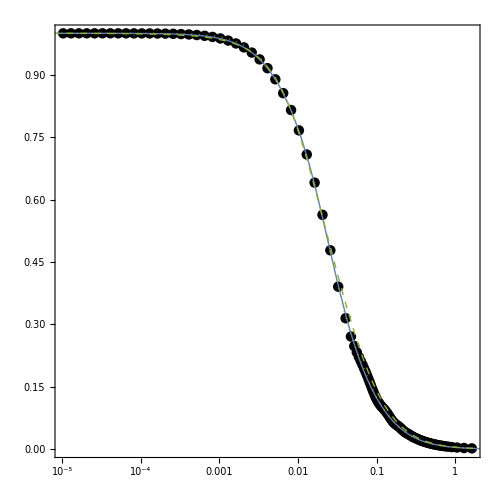

```mathematica
LogLinearPlot[{Winner[x,y,z],TEH[x*h,y,z],TcbBBKS[x*h,y,z,h,Neff]}/.y->NormPartData⟦10⟧⟦1,2⟧/.z->NormPartData⟦10⟧⟦1,3⟧//Evaluate,{x,5*10^-6,5},PlotRange->All,PlotStyle->{Directive[Thick],Directive[Thick,Dotted],Directive[Thick,Dashed]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH Formula}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,10}],
{0.23,0.15}],ImageSize->500];
ListPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->{{NormPartData⟦10⟧⟦1,1⟧,NormPartData⟦10⟧⟦-1,1⟧},All},ScalingFunctions->{"Log","Linear"},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Black,PointSize[0.015]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{CLASS}"]}],
{0.195,0.29}],ImageSize->500];
Plot1=Show[%,%%,ImageSize->500]
```

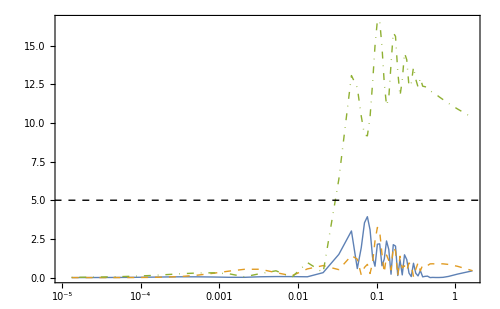

```mathematica
Plot2=ListLogLinearPlot[{Take[accGA,{10*57+1,11*57}],Take[accEH,{10*57+1,11*57}],Take[accBBKS,{10*57+1,11*57}]},Joined->True,PlotRange->{{NormPartData⟦10⟧⟦1,1⟧,NormPartData⟦10⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\%\\text{Acc}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Directive[Thick],Directive[Thick,Dashed],Directive[Thick,DotDashed]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH Formula}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5},LegendFunction->"Frame"],
{0.23,0.77}],Epilog->{{Dashed,Line[{{Log[10^-6],5},{Log[2],5}}]}},ImageSize->500]
```

# Transfer Function: Neutrinos

```mathematica
Quit[]
```

## Mock Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[16]; (* To use all the available kernels *)
```

### Data

```mathematica
DataTransferFunction=Import["Transfer_Function_Neutrinos.txt","Data"]//Quiet; (* Data from CLASS (python): {k, ωb, ωm, ων} *)
Length[DataTransferFunction]/114//N (* There are 64 lists *)
PartData=Partition[DataTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each triad {ωb, ωm, ων}*)
(* Modify data to get a squared normalized T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,((#⟦5⟧)/Max[PartData⟦i,1,5⟧])^2}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Drop[Drop[Drop[Join@@NormPartData,{1,-1,2}],{1,-1,2}],{1,-1,2}]; (* Drop some data points and re-join the sub-datasets *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

64.

{912,5}

### Eisenstein-Hu Fitting Formula: Massive Neutrinos

All the formulas are extracted from EH97I  [9710252] paper, unless stated.

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
h=0.67810; (* Reduced Hubble constant *)
ΩΛ=0.685; (* Density parameter of dark energy *)
z0=0; (* Redshift today *)
Nν=1; (* Number of massive neutrinos *)
zeqν[Ωm_,Ων_,h_]:=2.5*10^4(Ωm+Ων)h^2*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (1) *)
(* Redshift at drag epoch -> See Eq. (2) *)
b1dν[Ωm_,Ων_,h_]:=0.313((Ωm+Ων)h^2)^-0.419(1+0.607((Ωm+Ων)h^2)^0.674) 
b2dν[Ωm_,Ων_,h_]:=0.238((Ωm+Ων)h^2)^0.223 
zdν[Ωb_,Ωm_,Ων_,h_]:=1291*(((Ωm+Ων)h^2)^0.251)/(1+0.659((Ωm+Ων)h^2)^0.828)(1+b1dν[Ωm,Ων,h](Ωb*h^2)^b2dν[Ωm,Ων,h]) 
yEHν[z_,Ωm_,Ων_,h_]:=(1+zeqν[Ωm,Ων,h])/(1+z) (* Eq.(3) -> Useful variable for calculations in LS limit -> See Eq. (8.20) in Dodelson 2 *)
sν[Ωb_,Ωm_,Ων_,h_]:=(44.5Log[9.83/((Ωm+Ων)h^2)])/(√(1+10(Ωb*h^2)^(3/4))) (* Mpc *)(* Sound horizon at drag epoch -> See Eq. (4) *)
qν[k_,Ωm_,Ων_,h_]:=k*Θ^2((Ωm+Ων)h^2)^-1(* Mpc… See Eq. (5) *)
(* See Eq.(9)*)
g[z_,Ωm_,Ων_,ΩΛ_]:=√((Ωm+Ων)(1+z)^3+(1-Ωm-Ων-ΩΛ)(1+z)^2+ΩΛ)
(* See Eq.(10)*)
Ω[z_,Ωm_,Ων_,ΩΛ_]:=(Ωm+Ων)(1+z)^3 g[z,Ωm,Ων,ΩΛ]^-2
ΩΛf[z_,Ωm_,Ων_,ΩΛ_]:=ΩΛ*g[z,Ωm,Ων,ΩΛ]^-2
D1[z_,Ωm_,Ων_,ΩΛ_,h_]:=((1+zeqν[Ωm,Ων,h])/(1+z))*(5Ω[z,Ωm,Ων,ΩΛ])/2(Ω[z,Ωm,Ων,ΩΛ]^(4/7)-ΩΛf[z,Ωm,Ων,ΩΛ]+(1+Ω[z,Ωm,Ων,ΩΛ]/2)(1+ΩΛf[z,Ωm,Ων,ΩΛ]/70))^-1 
pcb[Ωm_,Ων_]:=1/4(5-√(1+24fcb[Ωm,Ων])) (* Eq.(11) *)
fcb[Ωm_,Ων_]:=Ωm/(Ωm+Ων)
fν[Ωm_,Ων_]:=Ων/(Ωm+Ων)
yfs[k_,Ωm_,Ων_,h_,Nν_]:=17.2*fν[Ωm,Ων](1+0.488*fν[Ωm,Ων]^(-7/6))*((Nν*qν[k,Ωm,Ων,h])/fν[Ωm,Ων])^2 (* Eq.(14) *) 
Dcbν[k_,z_,Ωm_,Ων_,ΩΛ_,h_,Nν_]:=(fcb[Ωm,Ων]^(0.7/pcb[Ωm,Ων])+(D1[z,Ωm,Ων,ΩΛ,h]/(1+yfs[k,Ωm,Ων,h,Nν]))^0.7)^(pcb[Ωm,Ων]/0.7)D1[z,Ωm,Ων,ΩΛ,h]^(1-pcb[Ωm,Ων]) (* Eq.(13) *)
qνν[k_,Ωm_,Ων_,h_,Nν_]:=3.92qν[k,Ωm,Ων,h]*√(Nν/fν[Ωm,Ων])(* Eq.(23) *)
B[k_,Ωm_,Ων_,h_,Nν_]:=1+(1.24 fν[Ωm,Ων]^0.64*Nν^(0.3+(0.6fν[Ωm,Ων])))/(qνν[k,Ωm,Ων,h,Nν]^-1.6+qνν[k,Ωm,Ων,h,Nν]^0.8) (* Eq.(22) *)
fνb[Ωb_,Ωm_,Ων_]:=(Ωb+Ων)/(Ωm+Ων)
βcν[Ωb_,Ωm_,Ων_]:=(1-0.949fνb[Ωb,Ωm,Ων])^-1(* Eq.(21) *)
C0[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=14.4+325/(1+60.5 qeff[k,Ωb,Ωm,Ων,h,Nν]^1.08)(* Eq.(20) *)
fc[Ωb_,Ωm_,Ων_]:=(Ωm-Ωb)/(Ωm+Ων)
pc[Ωb_,Ωm_,Ων_] :=1/4(5-√(1+24fc[Ωb,Ωm,Ων])) 
αν[Ωb_,Ωm_,Ων_,h_,Nν_]:=fc[Ωb,Ωm,Ων]/fcb[Ωm,Ων]*(5-2(pc[Ωb,Ωm,Ων]+pcb[Ωm,Ων]))/(5-4pcb[Ωm,Ων])*(1-0.553fνb[Ωb,Ωm,Ων]+0.126 fνb[Ωb,Ωm,Ων]^3)/(1-0.193 √(fν[Ωm,Ων]Nν)+0.169fν[Ωm,Ων] Nν^0.2) *(1+yEHν[zdν[Ωb,Ωm,Ων,h],Ωm,Ων,h])^(pcb[Ωm,Ων]-pc[Ωb,Ωm,Ων])*(1+(pc[Ωb,Ωm,Ων]-pcb[Ωm,Ων])/2(1+1/((3-4pc[Ωb,Ωm,Ων])(7-4pcb[Ωm,Ων])))(1+yEHν[zdν[Ωb,Ωm,Ων,h],Ωm,Ων,h])^-1)(* Eq.(15) *)
Γeff[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=(Ωm+Ων)h^2(√αν[Ωb,Ωm,Ων,h,Nν]+(1-√αν[Ωb,Ωm,Ων,h,Nν])/(1+(0.43 k*sν[Ωb,Ωm,Ων,h])^4)) (* Eq.(16) *)
qeff[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=(k*Θ^2)/Γeff[k,Ωb,Ωm,Ων,h,Nν](* Mpc… Eq.(17) *)
L[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=Log[ⅇ+1.84βcν[Ωb,Ωm,Ων] √αν[Ωb,Ωm,Ων,h,Nν] qeff[k,Ωb,Ωm,Ων,h,Nν]](* Eq.(19) *)
Tsup[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=L[k,Ωb,Ωm,Ων,h,Nν]/(L[k,Ωb,Ωm,Ων,h,Nν]+C0[k,Ωb,Ωm,Ων,h,Nν]*qeff[k,Ωb,Ωm,Ων,h,Nν]^2)(* Eq.(18) *) 
Tmaster[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=Tsup[k,Ωb,Ωm,Ων,h,Nν]*B[k,Ωm,Ων,h,Nν]
Tcbν[k_,Ωb_,Ωm_,Ων_,z_,ΩΛ_,h_,Nν_]:=Tmaster[k,Ωb,Ωm,Ων,h,Nν] Dcbν[k,z,Ωm,Ων,ΩΛ,h,Nν]/D1[z,Ωm,Ων,ΩΛ,h](* See Eq.(7) *)
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
length=4; depth=4; (* Number of nucleotides and genes. Chromosomes will be 4x4 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,9}; (* Power of x *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{w->#1,x->#2,y->#3,z->#4})&; (* Individual *)
temp=Mean[Table[Abs[MockData⟦i,5⟧-ft[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧,MockData⟦i,4⟧]]/MockData⟦i,5⟧*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4]]; (* If rep⟦2⟧ == 4 -> modify the power of x *)
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals": Σ r f((ax)^l(by)^m(cx)^n) -> See Eq. (10) *)
funcGA[w_,x_,y_,z_,kid_,gram_]:=Sum[kid⟦i,1⟧ gram⟦kid⟦i,2⟧⟧@((kid⟦i,3⟧w)^kid⟦i,4⟧),{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4]},{pop},{length}];
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for a function which is positive, goes to 1 when k -> 0, and k lives in a log-space -> See Eq. (9) *)
Do[
pigs=(1+funcGA[(2.3481818868485798w)/(y-x+z),x,y,z,#,grammar])^(-1/2)&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=100;
SaveState={};
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.7,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State_Neutrinos.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 51.854705

Time: 104.06263

Time: 156.31126

Time: 205.17424

Time: 257.88195

Time: 316.13546

Time: 370.094143

Time: 417.922959

Time: 473.870636

Time: 524.545231

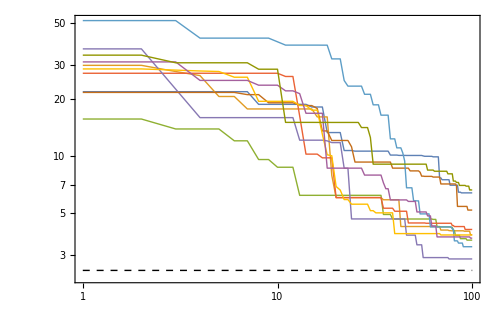

```mathematica
(* Plot the accuracy of GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1,generations},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\text{Acc}"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->True,PlotStyle->Thick,ImageSize->500,
Epilog->{{Dashed,Line[{{1,2.49642},{generations,2.49642}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.75,0.2}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.11}]]}]
```

```mathematica
DataSaved=Import["Save_State_Neutrinos.txt","Data"];
```

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-2.86842,6170}

```mathematica
AccGA[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧] (* Accuracy of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.x->0.022/.y-> 0.11/.z->0.0001,w->0] (* Correct limits of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.x->0.022/.y-> 0.11/.z->0.0001,w->∞]
```

2.86842

1.

0.

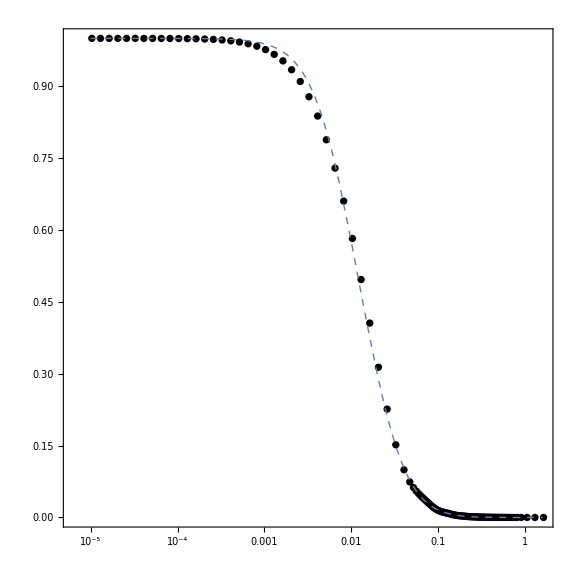

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{GApop1[PosElite⟦1,1⟧]⟦-1,2⟧/.x->NormPartData⟦5⟧⟦1,2⟧/.y->NormPartData⟦5⟧⟦1,3⟧/.z->NormPartData⟦5⟧⟦1,4⟧}//Evaluate,{w,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦5⟧⟦i,1⟧,NormPartData⟦5⟧⟦i,5⟧},{i,1,Length[NormPartData⟦5⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick,Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->Large]
```

### Long Run For the Winner

```mathematica
generations=10000;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[3702,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 2961 secs or 49 mins

Accuracy = 1.81151

Best-fit function is:

1/(√(1+56.4933 (w/(-x+y+z))^1.48261+3559.23 (w/(-x+y+z))^3.76407+4982.44 (w/(-x+y+z))^5.68246+374.167 (w/(-x+y+z))^7.14558))

```mathematica
(* Check the correct limits of the GA solution *)
Limit[GApop⟦-1,2⟧/.x->0.022/.y->0.11/.z->0.001,w->0]
Limit[GApop⟦-1,2⟧/.x->0.022/.y->0.11/.z->0.001,w->∞]
```

1.

0.

```mathematica
AccGA[GApop⟦-1,2⟧]
AccGA[Tcbν[w*h,x*h^-2,y*h^-2,z*h^-2,z0,ΩΛ,h,Nν]^2]
```

1.81151

2.49642

```mathematica
Export["Accuracy_Evolution_Neutrinos.txt",GApop⟦All,1⟧,"Table"];
```

### Plots

```mathematica
Winner[w_,x_,y_,z_]:=1/(√(1+56.49330091650579 (w/(-x+y+z))^1.4826111693304167+3559.2345746346377 (w/(-x+y+z))^3.7640671710781763+4982.439615150513 (w/(-x+y+z))^5.682456032609869+374.1673278547184 (w/(-x+y+z))^7.145575959922812))
DataAccuracy=Import["Accuracy_Evolution_Neutrinos.txt","Data"]//Flatten;
```

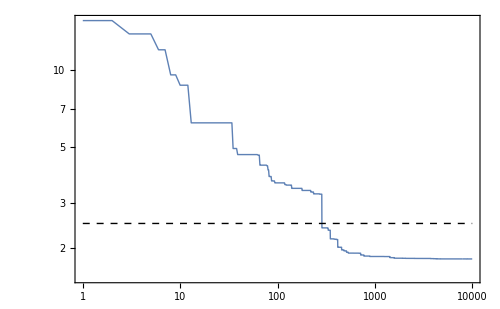

```mathematica
(* Plot of χ^2 over the generations -> We should modify the configuration of the GA *)
generations=10000;
ListLogLogPlot[GApop⟦All,1⟧//Abs,Joined->True,
PlotRange->{{1,generations},All},PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500,
Epilog->{{Dashed,Line[{{1,2.4964},{generations,2.4964}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.28}]]}]
```

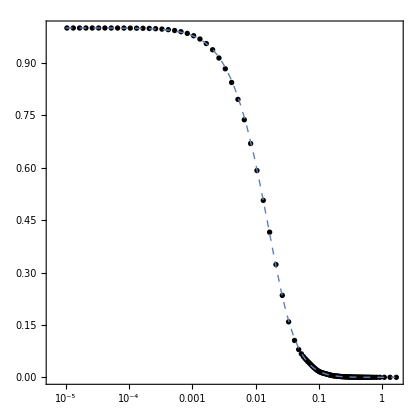

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{Winner[w,x,y,z]}/.x->NormPartData⟦10⟧⟦1,2⟧/.y->NormPartData⟦10⟧⟦1,3⟧/.z->NormPartData⟦10⟧⟦1,4⟧//Evaluate,{w,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,5⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->False,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%,ImageSize->420]
```

```mathematica
(* Accuracy for each T^2(k); there are 64 datasets *)
AccuracyWinner=Table[Mean[Table[{Abs[NormPartData⟦j⟧⟦i,5⟧-Winner[NormPartData⟦j⟧⟦i,1⟧,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧,NormPartData⟦j⟧⟦1,4⟧]]/(NormPartData⟦j⟧⟦i,5⟧)*100},{i,1,Length[NormPartData⟦j⟧]}]],{j,1,Length[NormPartData]}]
```

{{2.58909},{1.92076},{1.74903},{2.17455},{2.48731},{1.85074},{1.55486},{1.9226},{2.441},{1.81883},{1.4055},{1.71331},{2.42946},{1.83045},{1.34963},{1.56052},{2.46387},{1.86565},{1.91932},{2.42184},{2.34161},{1.75644},{1.69721},{2.14859},{2.2794},{1.69685},{1.51178},{1.90929},{2.25027},{1.68013},{1.37973},{1.73089},{2.36433},{1.88016},{2.12269},{2.67768},{2.21656},{1.70021},{1.87177},{2.38821},{2.13384},{1.60769},{1.66251},{2.13371},{2.09297},{1.55885},{1.49626},{1.92511},{2.30919},{2.01168},{2.35297},{2.94207},{2.12213},{1.76947},{2.08246},{2.63287},{2.00901},{1.59556},{1.85186},{2.36653},{1.94387},{1.477},{1.65152},{2.1396}}

## Comparison

```mathematica
(* Compare with T(k) instead of T^2(k) using the complete dataset *)
DataLinearTransferFunction=Import["Transfer_Function_Neutrinos.txt","Data"]//Quiet; (* Data from CLASS (python): {k, ωb, ωm, ων} *)
LinearPartData=Partition[DataLinearTransferFunction,114]; (* Partition of data to consider each cosmology, i.e. each triad {ωb, ωm, ων}*)
LinearNormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,(#⟦5⟧)/Max[PartData⟦i,1,5⟧]}&/@LinearPartData⟦i⟧,{i,1,Length[LinearPartData]}]; 
LinearMockData=Join@@LinearNormPartData; (* Re-Join the sub-datasets *)
```

```mathematica
accEH=Table[{LinearNormPartData⟦18⟧⟦i,1⟧,100*Abs[(1-1/(LinearNormPartData⟦18⟧⟦i,5⟧)Tcbν[LinearNormPartData⟦18⟧⟦i,1⟧*h,LinearNormPartData⟦18⟧⟦i,2⟧*h^-2,LinearNormPartData⟦18⟧⟦i,3⟧*h^-2,LinearNormPartData⟦18⟧⟦i,4⟧*h^-2,z0,ΩΛ,h,Nν])]},{i,1,Length[LinearNormPartData⟦18⟧]}];
accGA=Table[{LinearNormPartData⟦18⟧⟦i,1⟧,100*Abs[(1-Winner[LinearNormPartData⟦18⟧⟦i,1⟧,LinearNormPartData⟦18⟧⟦i,2⟧,LinearNormPartData⟦18⟧⟦i,3⟧,LinearNormPartData⟦18⟧⟦i,4⟧]^(1/2)/(LinearNormPartData⟦18⟧⟦i,5⟧))]},{i,1,Length[LinearNormPartData⟦18⟧]}];
```

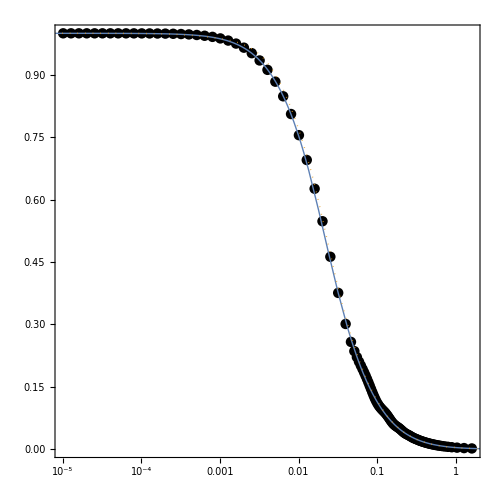

```mathematica
LogLinearPlot[{Winner[w,x,y,z]^(1/2),Tcbν[w*h,x*h^-2,y*h^-2,z*h^-2,z0,ΩΛ,h,Nν]}/.x->LinearNormPartData⟦18⟧⟦1,2⟧/.y->LinearNormPartData⟦18⟧⟦1,3⟧/.z->LinearNormPartData⟦18⟧⟦1,4⟧//Evaluate,{w,5*10^-6,5},PlotRange->All,PlotStyle->{Directive[Thick],Directive[Thick,Dotted],Directive[Thick,Dashed]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH Formula}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,10}],
{0.23,0.15}],ImageSize->500];
ListPlot[Table[{LinearNormPartData⟦18⟧⟦i,1⟧,LinearNormPartData⟦18⟧⟦i,5⟧},{i,1,Length[LinearNormPartData⟦18⟧]}],Joined->False,PlotRange->{{LinearNormPartData⟦18⟧⟦1,1⟧,LinearNormPartData⟦18⟧⟦-1,1⟧},All},ScalingFunctions->{"Log","Linear"},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Black,PointSize[0.015]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{CLASS}"]}],
{0.215,0.27}],ImageSize->500];
Plot3=Show[%,%%,ImageSize->500]
```

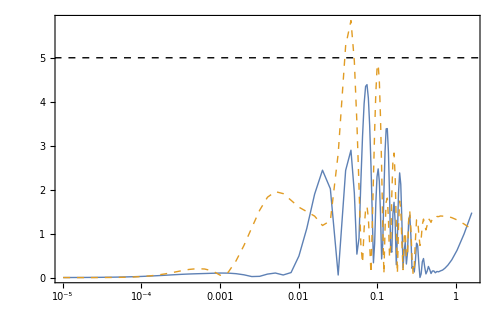

```mathematica
Plot4=ListLogLinearPlot[{accGA,accEH},Joined->True,PlotRange->{{NormPartData⟦18⟧⟦1,1⟧,NormPartData⟦18⟧⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\%\\text{Acc}"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Directive[Thick],Directive[Thick,Dashed],Directive[Thick,DotDashed]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA Solution}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH Formula}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,5},LegendFunction->"Frame"],
{0.23,0.5}],Epilog->{{Dashed,Line[{{Log[10^-6],5},{Log[2],5}}]}},ImageSize->500]
```

```mathematica
TotAccEH=Mean[Table[{Abs[LinearMockData⟦i,5⟧-Tcbν[LinearMockData⟦i,1⟧*h,LinearMockData⟦i,2⟧*h^-2,LinearMockData⟦i,3⟧*h^-2,LinearMockData⟦i,4⟧*h^-2,z0,ΩΛ,h,Nν]]/LinearMockData⟦i,5⟧*100},{i,1,Length[LinearMockData]}]]
TotAccGA=Mean[Table[{Abs[LinearMockData⟦i,5⟧-Winner[LinearMockData⟦i,1⟧,LinearMockData⟦i,2⟧,LinearMockData⟦i,3⟧,LinearMockData⟦i,4⟧]^(1/2)]/LinearMockData⟦i,5⟧*100},{i,1,Length[LinearMockData]}]]
```

{1.23449}

{0.993916}

```mathematica
(* Accuracy for each T(k) -> there are 64 datasets *)
LinearAccuracyWinner=Table[Mean[Table[{Abs[LinearNormPartData⟦j⟧⟦i,5⟧-Winner[LinearNormPartData⟦j⟧⟦i,1⟧,LinearNormPartData⟦j⟧⟦1,2⟧,LinearNormPartData⟦j⟧⟦1,3⟧,LinearNormPartData⟦j⟧⟦1,4⟧]^(1/2)]/(LinearNormPartData⟦j⟧⟦i,5⟧)*100},{i,1,Length[LinearNormPartData⟦j⟧]}]],{j,1,Length[LinearNormPartData]}]
```

{{1.30954},{0.967815},{0.876265},{1.08256},{1.25705},{0.931777},{0.77879},{0.95728},{1.23282},{0.915147},{0.703838},{0.853257},{1.22634},{0.920538},{0.675675},{0.777309},{1.24562},{0.939357},{0.960265},{1.20424},{1.18272},{0.883616},{0.848903},{1.0685},{1.15041},{0.853052},{0.756017},{0.949678},{1.13503},{0.84419},{0.689865},{0.86116},{1.19472},{0.945777},{1.06061},{1.32994},{1.11891},{0.854592},{0.93494},{1.18627},{1.07622},{0.807493},{0.830254},{1.06005},{1.05487},{0.782503},{0.747134},{0.956672},{1.16618},{1.01066},{1.17421},{1.45966},{1.07057},{0.888327},{1.03883},{1.3063},{1.01257},{0.800525},{0.923601},{1.17436},{0.978985},{0.740637},{0.823577},{1.06205}}